## Now for five and real colofours

```mathematica
MyColors=Association[];
```

```mathematica
MyColors[Greater]=Green;MyColors[GreaterEqual]=Orange;MyColors[Equal]=Red;MyColors
```

<|Greater→RGBColor[0, 1, 0],GreaterEqual→RGBColor[1, 0.5, 0],Equal→RGBColor[1, 0, 0]|>

```mathematica
ChangeSYmbol[s_]:=Symbol["n"<>StringDrop[SymbolName[s],1]]
```

```mathematica
vertexLabels=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofournull"]]-> Tooltip[Style[Rotate[allGraphs5[k,"atleast"],Pi/4],Red,Bold,14],Labeled[ShowGraph[allGraphs5,k],allGraphs5[k,"compwhy"]]],{k,Sort[allGraphs5FakeAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→36,n1x2x3x45→23,n1x2x35x4→26,n1x2x34x5→23,n1x2x345→10,n1x25x3x4→26,n1x25x34→17,n1x24x3x5→26,n1x24x35→18,n1x245x3→11,n1x23x4x5→23,n1x23x45→15,n1x235x4→11,n1x234x5→10,n1x2345→2,n15x2x3x4→23,n15x2x34→15,n15x24x3→17,n15x23x4→15,n15x234→7,n14x2x3x5→26,n14x2x35→18,n14x25x3→18,n14x23x5→17,n14x235→7,n145x2x3→10,n145x23→7,n13x2x4x5→26,n13x2x45→17,n13x25x4→18,n13x24x5→18,n13x245→7,n135x2x4→11,n135x24→7,n134x2x5→11,n134x25→7,n1345x2→2,n12x3x4x5→23,n12x3x45→15,n12x35x4→17,n12x34x5→15,n12x345→7,n125x3x4→10,n125x34→7,n124x3x5→11,n124x35→7,n1245x3→2,n123x4x5→10,n123x45→7,n1235x4→2,n1234x5→2,n12345→0}

```mathematica
vertexStyle=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofournull"]]-> MyColors[allGraphs5[k,"comp"]],{k,Sort[allGraphs5FakeAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→RGBColor[0, 1, 0],n1x2x3x45→RGBColor[0, 1, 0],n1x2x35x4→RGBColor[0, 1, 0],n1x2x34x5→RGBColor[0, 1, 0],n1x2x345→RGBColor[0, 1, 0],n1x25x3x4→RGBColor[0, 1, 0],n1x25x34→RGBColor[0, 1, 0],n1x24x3x5→RGBColor[0, 1, 0],n1x24x35→RGBColor[0, 1, 0],n1x245x3→RGBColor[0, 1, 0],n1x23x4x5→RGBColor[0, 1, 0],n1x23x45→RGBColor[0, 1, 0],n1x235x4→RGBColor[0, 1, 0],n1x234x5→RGBColor[0, 1, 0],n1x2345→RGBColor[0, 1, 0],n15x2x3x4→RGBColor[0, 1, 0],n15x2x34→RGBColor[0, 1, 0],n15x24x3→RGBColor[0, 1, 0],n15x23x4→RGBColor[0, 1, 0],n15x234→RGBColor[0, 1, 0],n14x2x3x5→RGBColor[0, 1, 0],n14x2x35→RGBColor[0, 1, 0],n14x25x3→RGBColor[0, 1, 0],n14x23x5→RGBColor[0, 1, 0],n14x235→RGBColor[0, 1, 0],n145x2x3→RGBColor[0, 1, 0],n145x23→RGBColor[0, 1, 0],n13x2x4x5→RGBColor[0, 1, 0],n13x2x45→RGBColor[0, 1, 0],n13x25x4→RGBColor[0, 1, 0],n13x24x5→RGBColor[0, 1, 0],n13x245→RGBColor[0, 1, 0],n135x2x4→RGBColor[0, 1, 0],n135x24→RGBColor[0, 1, 0],n134x2x5→RGBColor[0, 1, 0],n134x25→RGBColor[0, 1, 0],n1345x2→RGBColor[0, 1, 0],n12x3x4x5→RGBColor[0, 1, 0],n12x3x45→RGBColor[0, 1, 0],n12x35x4→RGBColor[0, 1, 0],n12x34x5→RGBColor[0, 1, 0],n12x345→RGBColor[0, 1, 0],n125x3x4→RGBColor[0, 1, 0],n125x34→RGBColor[0, 1, 0],n124x3x5→RGBColor[0, 1, 0],n124x35→RGBColor[0, 1, 0],n1245x3→RGBColor[0, 1, 0],n123x4x5→RGBColor[0, 1, 0],n123x45→RGBColor[0, 1, 0],n1235x4→RGBColor[0, 1, 0],n1234x5→RGBColor[0, 1, 0],n12345→RGBColor[1, 0, 0]}

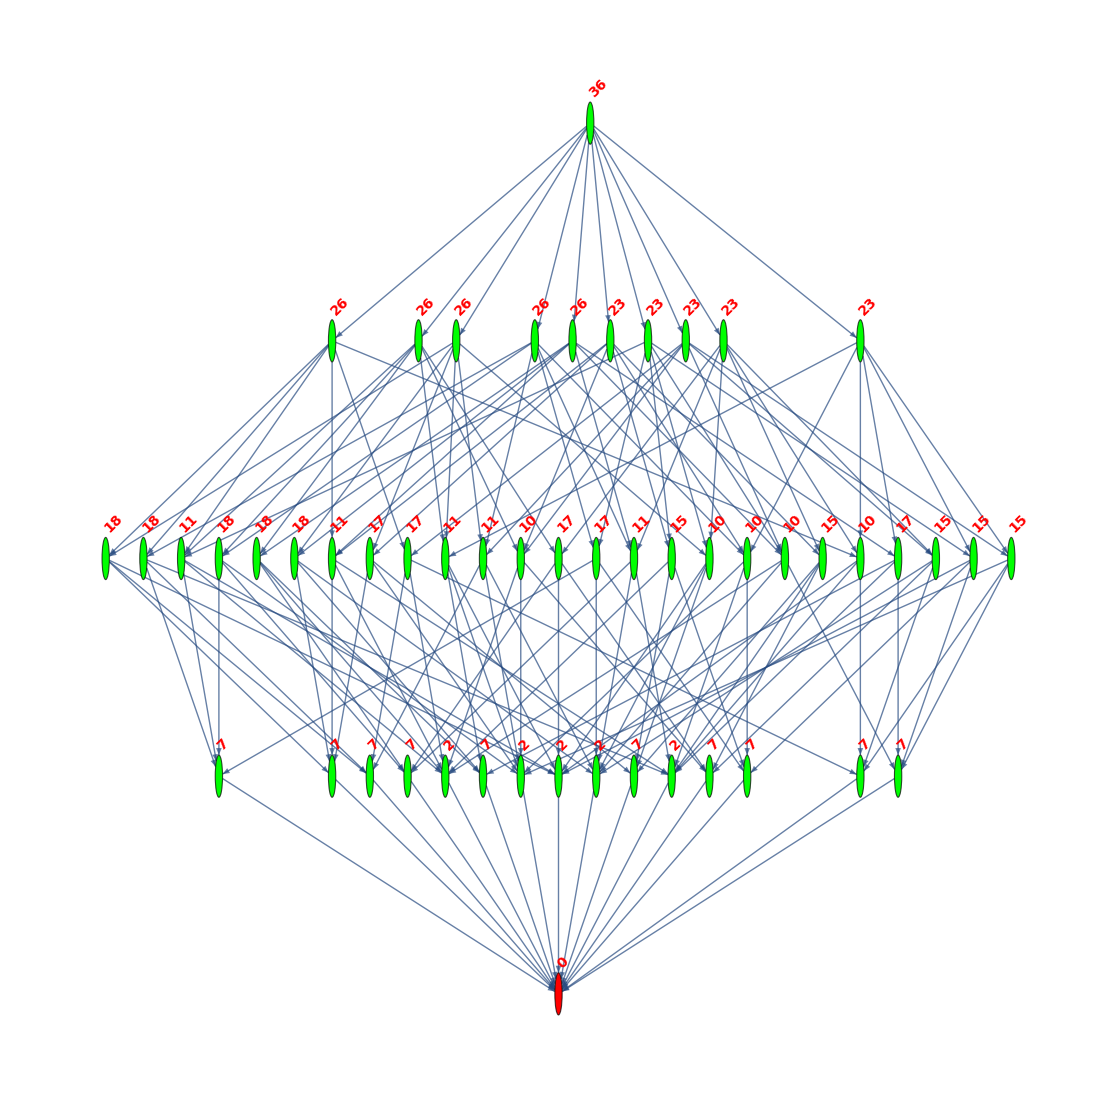

```mathematica
gr=Graph[EdgeList[MobiusGraph5[K5Key,allGraphs5]],VertexLabels->vertexLabels,GraphLayout->"LayeredDigraphEmbedding", VertexStyle->vertexStyle,AspectRatio->1]
```

```mathematica
repEmpty=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofournull"]]-> allGraphs5[k,"atleast"],{k,Sort[allGraphs5FakeAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→36,n1x2x3x45→23,n1x2x35x4→26,n1x2x34x5→23,n1x2x345→10,n1x25x3x4→26,n1x25x34→17,n1x24x3x5→26,n1x24x35→18,n1x245x3→11,n1x23x4x5→23,n1x23x45→15,n1x235x4→11,n1x234x5→10,n1x2345→2,n15x2x3x4→23,n15x2x34→15,n15x24x3→17,n15x23x4→15,n15x234→7,n14x2x3x5→26,n14x2x35→18,n14x25x3→18,n14x23x5→17,n14x235→7,n145x2x3→10,n145x23→7,n13x2x4x5→26,n13x2x45→17,n13x25x4→18,n13x24x5→18,n13x245→7,n135x2x4→11,n135x24→7,n134x2x5→11,n134x25→7,n1345x2→2,n12x3x4x5→23,n12x3x45→15,n12x35x4→17,n12x34x5→15,n12x345→7,n125x3x4→10,n125x34→7,n124x3x5→11,n124x35→7,n1245x3→2,n123x4x5→10,n123x45→7,n1235x4→2,n1234x5→2,n12345→0}

```mathematica
Sort[Table[((e[[2]]/e[[1]])/.repEmpty), {e,EdgeList[gr]}]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/9,1/9,1/9,1/9,1/9,2/17,2/17,2/17,2/17,2/17,2/15,2/15,2/15,2/15,2/15,2/11,2/11,2/11,2/11,2/11,2/11,2/11,2/11,2/11,2/11,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,1/5,5/13,5/13,5/13,5/13,5/13,7/18,7/18,7/18,7/18,7/18,7/18,7/18,7/18,7/18,7/18,7/17,7/17,7/17,7/17,7/17,7/17,7/17,7/17,7/17,7/17,11/26,11/26,11/26,11/26,11/26,11/26,11/26,11/26,11/26,11/26,10/23,10/23,10/23,10/23,10/23,10/23,10/23,10/23,10/23,10/23,7/15,7/15,7/15,7/15,7/15,7/15,7/15,7/15,7/15,7/15,11/23,11/23,11/23,11/23,11/23,7/11,7/11,7/11,7/11,7/11,23/36,23/36,23/36,23/36,23/36,15/23,15/23,15/23,15/23,15/23,15/23,15/23,15/23,15/23,15/23,17/26,17/26,17/26,17/26,17/26,9/13,9/13,9/13,9/13,9/13,9/13,9/13,9/13,9/13,9/13,7/10,7/10,7/10,7/10,7/10,13/18,13/18,13/18,13/18,13/18,17/23,17/23,17/23,17/23,17/23}

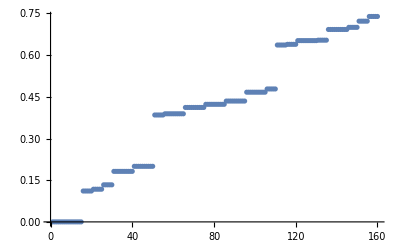

```mathematica
Table[((e[[2]]/e[[1]])/.repEmpty), {e,EdgeList[gr]}]//Sort//ListPlot
```

```mathematica
rep5Bis=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofourrealnull"]]-> allGraphs5[k,"atleast"],{k,Sort[allGraphs5NullAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→36,n1x2x3x45→13,n1x2x35x4→10,n1x2x34x5→13,n1x2x345→5,n1x25x3x4→10,n1x25x34→4,n1x24x3x5→10,n1x24x35→2,n1x245x3→4,n1x23x4x5→13,n1x23x45→5,n1x235x4→4,n1x234x5→5,n1x2345→2,n15x2x3x4→13,n15x2x34→5,n15x24x3→4,n15x23x4→5,n15x234→2,n14x2x3x5→10,n14x2x35→2,n14x25x3→2,n14x23x5→4,n14x235→1,n145x2x3→5,n145x23→2,n13x2x4x5→10,n13x2x45→4,n13x25x4→2,n13x24x5→2,n13x245→1,n135x2x4→4,n135x24→1,n134x2x5→4,n134x25→1,n1345x2→2,n12x3x4x5→13,n12x3x45→5,n12x35x4→4,n12x34x5→5,n12x345→2,n125x3x4→5,n125x34→2,n124x3x5→4,n124x35→1,n1245x3→2,n123x4x5→5,n123x45→2,n1235x4→2,n1234x5→2,n12345→1}

```mathematica
eq1=Simplify[Fold[And,Table[((e[[1]] >=e[[2]])/.rep5Bis), {e,EdgeList[gr]}]]]
```

True

```mathematica
eq2=Fold[
And,
Table[allGraphs5[k,"colofour"]≥ allGraphs5[k,"atleast"]
,{k,allGraphs5FakeAtomKeys}]//Flatten
];
```

```mathematica
Zero={alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,K5Key}
```

{36166,31738,29608,36112,31714,29524}

```mathematica
eq3=Fold[
And,
Table[
allGraphs5[k,"colofour"]==0
,{k,Zero}]//Flatten
]
```

v13x24x5==0&&v14x25x3==0&&v1x24x35==0&&v13x25x4==0&&v14x2x35==0&&v1x2x3x4x5==0

```mathematica
Length[long]
```

1895

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

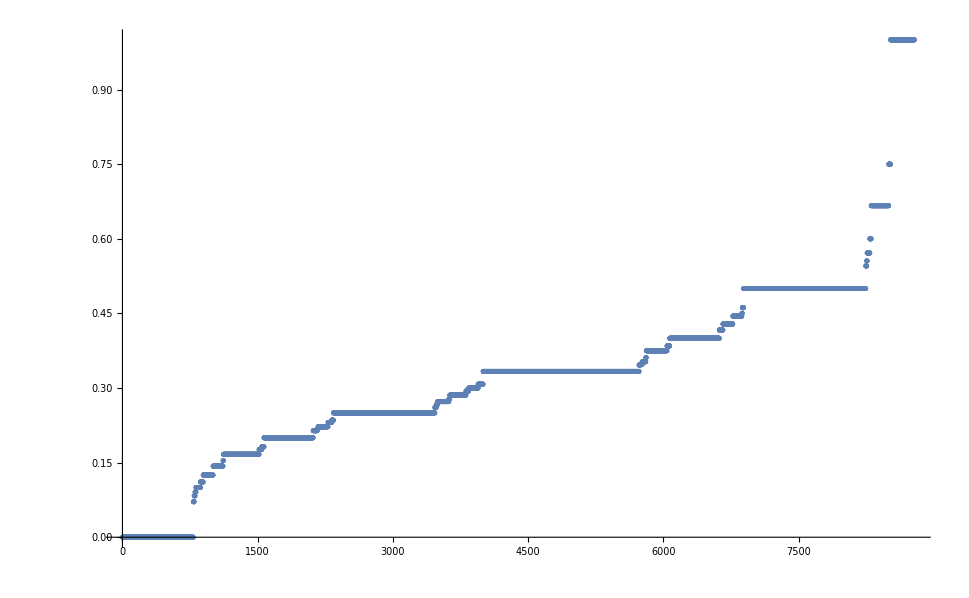

```mathematica
Table[
Table[
Table[
allGraphs5[child,"atleast"]/allGraphs5[k,"atleast"]
,{child,Rest[children]}
]
,{children,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
]//Flatten//Sort//ListPlot
```